```mathematica
(*This system will be a plate with a rod in the middle. 
This example will use Lie-Trotter Splitting
So the equation is F = R + V
R is the 2D plate without the rod
V is the 2D plate with the rod

Here is the pseudo-code:
Let F(0) = initV below
For t = 0,tau, 2tau,...,T
	 Let R(t) = F(t)
	Integrate R'(t) to obtain R(t+tau)
	Let V(t)=R(t+tau)
   Integrate V'(t) to obtain V(t+tau)
   Let F(t+tau)=V(t+tau) 	*)
```

```mathematica
initV[x_,y_]:=20*x(x-2)y(y-1)
```

```mathematica
Plot3D[initV[x,y],{x,0,2},{y,0,1}]
```

-Graphics3D-

```mathematica
alphaPlate = 0.05; alphaRod = 0.2;
```

```mathematica
maxT = 15; NN = 100; tau=maxT/NN; (*max time and num time steps respectively*)
```

```mathematica
u1vals = NDSolveValue[{{D[u[y,t],t]==alphaRod*D[u[y,t],{y,2}]},{u[y,0]==initV[1,y]},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,tau}]
```

InterpolatingFunction[{{0., 1.}, {0., 0.15}}, <>]

```mathematica
v1vals = NDSolveValue[{{D[v[x,y,t],t]==alphaPlate*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==-u1vals[y,tau]*x*(x-2)},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[2,y,t]==0}},v,{x,0,2},{y,0,1},{t,0,tau}]
```

InterpolatingFunction[{{0., 2.}, {0., 1.}, {0., 0.15}}, <>]

```mathematica
u2vals =NDSolveValue[{{D[u[y,t],t]==alphaRod*D[u[y,t],{y,2}]},{u[y,tau]==v1vals[1,y,tau]},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,tau,2*tau}]
```

InterpolatingFunction[{{0., 1.}, {0.15, 0.3}}, <>]

```mathematica
v2vals = NDSolveValue[{{D[v[x,y,t],t]==alphaPlate*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,tau]==-u2vals[y,2*tau]*x*(x-2)},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[2,y,t]==0}},v,{x,0,2},{y,0,1},{t,tau,2*tau}]
```

InterpolatingFunction[{{0., 2.}, {0., 1.}, {0.15, 0.3}}, <>]

```mathematica
list1 = Range[5]
```

{1,2,3,4,5}

```mathematica
AppendTo[list1,9]
```

{1,2,3,4,5,9}

```mathematica
Part[list1,5]
```

5

```mathematica
list1[[5]]
```

5

```mathematica
listR = Range[15]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
listV = Range[16,30]
```

{16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
listF={0}
```

{0}

```mathematica
Do[(rr = listF[[i]]; rr = rr + listR[[i]]; vv = listV[[i]]+rr; AppendTo[listF,vv]),{i,1,15}]
```

```mathematica
listF
```

{0,17,36,57,80,105,132,161,192,225,260,297,336,377,420,465}

```mathematica
initVals = NDSolveValue[{{y''[t]==-9.8},{y'[0]==0},{y[0]==0}},y,{t,0,10}]
```

InterpolatingFunction[{{0., 10.}}, <>]

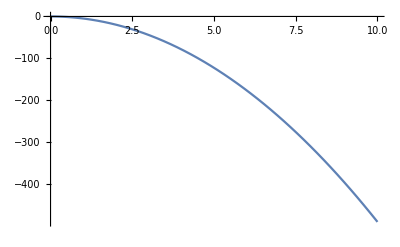

```mathematica
Plot[initVals[t],{t,0,10}]
```

```mathematica
listVV = {0}
```

{0}

```mathematica
listVeloc = {0}
```

{0}

```mathematica
Do[(curY = listVV[[i]]; 
curVeloc = listVeloc[[i]];
vals = NDSolveValue[{{y''[t]==-9.8},{y'[0]==curVeloc},{y[0]==curY}},y,{t,0,1}];
vals2 = NDSolveValue[{{vel'[t]==-9.8},{vel[0]==curVeloc}},vel,{t,0,1}];
AppendTo[listVeloc,vals2[1]];
AppendTo[listVV,vals[1]]),{i,1,10}]
```

```mathematica
listVV
```

{0,-4.9,-19.6,-44.1,-78.4,-122.5,-176.4,-240.1,-313.6,-396.9,-490.}

```mathematica
(*The above example shows how to combine lists, for loops, and PDE solving*)
(*In the below I will try to use the heat equation on a simple 1D rod*)
```

```mathematica
curT[y_]:=-20*y*(y-1)
```

```mathematica
Do[(tvals = NDSolveValue[{{D[u[y,t],t]==alphaRod*D[u[y,t],{y,2}]},{u[y,0]==curT[y]},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,1}];curT[y_] := tvals[y,1]
),{i,1,10}]
```

```mathematica
(*Here I need to take the above and see if I can make a list of tables*)
```

```mathematica
initTvals = Table[curT[i/100],{i,0,100}]
```

{0,99/500,49/125,291/500,96/125,19/20,141/125,651/500,184/125,819/500,9/5,979/500,264/125,1131/500,301/125,51/20,336/125,1411/500,369/125,1539/500,16/5,1659/500,429/125,1771/500,456/125,15/4,481/125,1971/500,504/125,2059/500,21/5,2139/500,544/125,2211/500,561/125,91/20,576/125,2331/500,589/125,2379/500,24/5,2419/500,609/125,2451/500,616/125,99/20,621/125,2491/500,624/125,2499/500,5,2499/500,624/125,2491/500,621/125,99/20,616/125,2451/500,609/125,2419/500,24/5,2379/500,589/125,2331/500,576/125,91/20,561/125,2211/500,544/125,2139/500,21/5,2059/500,504/125,1971/500,481/125,15/4,456/125,1771/500,429/125,1659/500,16/5,1539/500,369/125,1411/500,336/125,51/20,301/125,1131/500,264/125,979/500,9/5,819/500,184/125,651/500,141/125,19/20,96/125,291/500,49/125,99/500,0}

```mathematica
listOfVals = {initTvals}
```

{{0,99/500,49/125,291/500,96/125,19/20,141/125,651/500,184/125,819/500,9/5,979/500,264/125,1131/500,301/125,51/20,336/125,1411/500,369/125,1539/500,16/5,1659/500,429/125,1771/500,456/125,15/4,481/125,1971/500,504/125,2059/500,21/5,2139/500,544/125,2211/500,561/125,91/20,576/125,2331/500,589/125,2379/500,24/5,2419/500,609/125,2451/500,616/125,99/20,621/125,2491/500,624/125,2499/500,5,2499/500,624/125,2491/500,621/125,99/20,616/125,2451/500,609/125,2419/500,24/5,2379/500,589/125,2331/500,576/125,91/20,561/125,2211/500,544/125,2139/500,21/5,2059/500,504/125,1971/500,481/125,15/4,456/125,1771/500,429/125,1659/500,16/5,1539/500,369/125,1411/500,336/125,51/20,301/125,1131/500,264/125,979/500,9/5,819/500,184/125,651/500,141/125,19/20,96/125,291/500,49/125,99/500,0}}

```mathematica
Do[(tvals = NDSolveValue[{{D[u[y,t],t]==alphaRod*D[u[y,t],{y,2}]},{u[y,0]==curT[y]},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,1}];curT[y_] := tvals[y,1];
curTvals = Table[curT[jj/100],{jj,1,100}];
AppendTo[listOfVals,curTvals]
),{ii,1,10}]
```

```mathematica
Manipulate[ListPlot[{listOfVals[[ii]],Table[5,{i,100}]}],{ii,1,10,1}]
```

Part::partd: Part specification listOfVals⟦2⟧ is longer than depth of object.

```mathematica
uvalsOriginal = NDSolveValue[{{D[u[y,t],t]==alphaRod*D[u[y,t],{y,2}]},{u[y,0]==-20*y*(y-1)},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,10}]
```

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
Manipulate[Plot[{uvalsOriginal[y,t],5},{y,0,1}],{t,0,10}]
```

```mathematica
(*Attempting the above but with 2D function*)
```

```mathematica
vvalsOriginal = NDSolveValue[{{D[v[x,y,t],t]==alphaPlate*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==20*x(x-2)y(y-1)},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[2,y,t]==0}},v,{x,0,2},{y,0,1},{t,0,10}]
```

InterpolatingFunction[{{0., 2.}, {0., 1.}, {0., 10.}}, <>]

```mathematica
curTv[x_,y_]:=20*x(x-2)y(y-1)
```

```mathematica
initTvVals = Table[curTv[i/100,j/100],{i,0,200},{j,0,100}];
```

```mathematica
allTvVals = {initTvVals};
```

```mathematica
Do[
(tvvalues = NDSolveValue[{{D[v[x,y,t],t]==alphaPlate*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==curTv[x,y]},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[2,y,t]==0}},v,{x,0,2},{y,0,1},{t,0,1}];curTv[x_,y_] := tvvalues[x,y,1];
curTvvalues = Table[curTv[ii/100,jj/100],{ii,1,200},{jj,1,100}];
AppendTo[allTvVals,curTvvalues]
),{iii,1,10}]
```

```mathematica
Manipulate[ListPlot3D[{allTvVals[[jjj]],Table[5,{i,200},{j,100}]}],{jjj,1,11,1}]
```

```mathematica
Manipulate[Plot3D[{vvalsOriginal[x,y,t],5},{x,0,2},{y,0,1}],{t,0,10,1}]
```